```mathematica
SetDirectory[NotebookDirectory[]<>"..\\2009\\results"]
```

D:\Работа\Programs\speed\2009\results

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\2005\\results"]
```

D:\Работа\Programs\speed\2005\results

```mathematica
ReadData[name_]:=Block[{st=OpenRead[name],dump={1},meshs,test},Read[st,String];While[Last[dump]=!=EndOfFile,AppendTo[dump,Read[st,Number]];Skip[st,Character,24];AppendTo[dump,Read[st,Number]];Skip[st,Character,12];AppendTo[dump,Read[st,Number]];Skip[st,Character,12];AppendTo[dump,Read[st,Number]];Skip[st,Character,15];AppendTo[dump,Read[st,Number]];Skip[st,String];];Close[st];dump;dump=Partition[Select[Rest[dump],NumericQ],5];
meshs=Union[Last/@dump];
test=Map[Function[mesh,Sort[Select[dump,Last[#1]==mesh&]]],meshs];
Return[test];];
ShowRel[l_,iter_:False]:=Block[{Iter1=((#1⟦4⟧)/(#1⟦2⟧)&)[l⟦1⟧],Total1=l⟦1,4⟧,byIter,byTotal},
byIter=({#1⟦1⟧,Iter1/((#1⟦4⟧)/(#1⟦2⟧))}&)/@l;byTotal=({#1⟦1⟧,Total1/(#1⟦4⟧)}&)/@l;If[iter,ListPlot[byIter,Joined->True,PlotLabel->"Time per 1 iteration on mesh "<>ToString[Last[l⟦1⟧]]<>"^3",PlotRange->All,AxesOrigin->{1,0}],ListPlot[byTotal,Joined->True,PlotLabel->"Total time on mesh"<>ToString[Last[l⟦1⟧]]<>"^3",PlotRange->All,AxesOrigin->{1,0}]];
ListPlot[byIter,Joined->True,PlotLabel->"Acceleration on mesh  "<>ToString[Last[l⟦1⟧]]<>"^3",PlotRange->All,AxesOrigin->{1,0},PlotMarkers->●]];
```

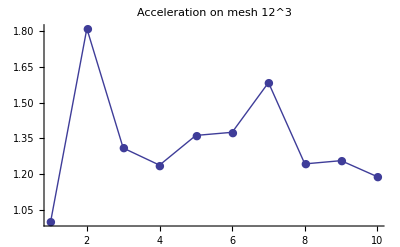
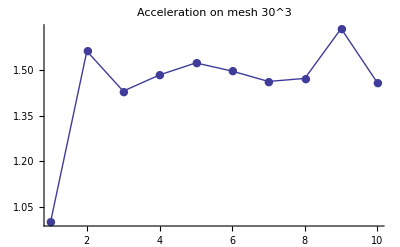
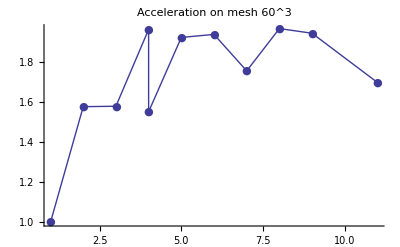
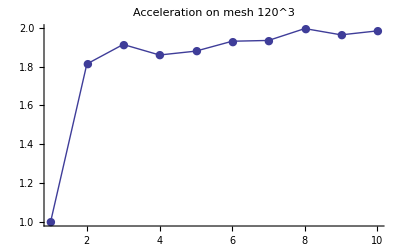

```mathematica
resAmazonka=ReadData["result(Amazonka).dat"];
grAmazonka=ShowRel[#,True]&/@resAmazonka
```

```mathematica
Manipulate[ListPlot[{#⟦1⟧,(#1⟦4⟧#⟦1⟧)/(#1⟦2⟧)}&/@{resTopsy,resIMM64,resPSTU}[[nl,nd]]],{nl,Range[3]},{nd,Range[4]}]
```

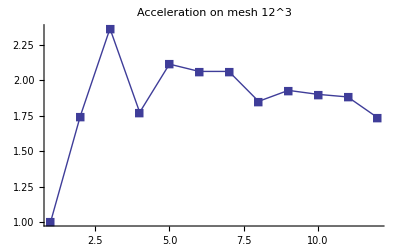
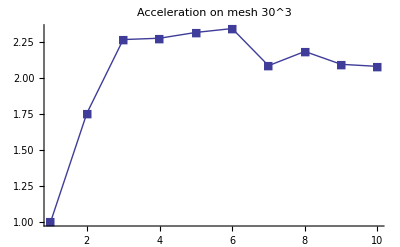
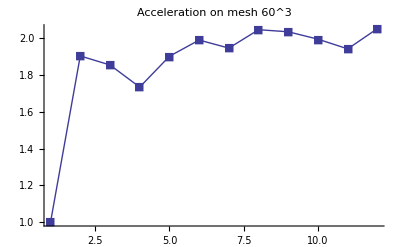
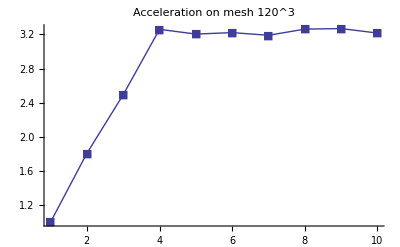

```mathematica
resTopsy=ReadData["result(Topsy).dat"];
grTopsy=ReplaceAll[ShowRel[#,True]&/@resTopsy,●->■]
```

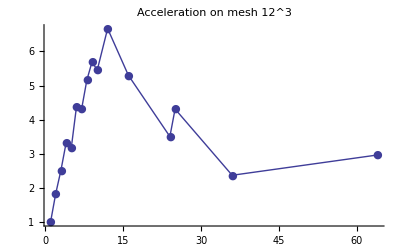
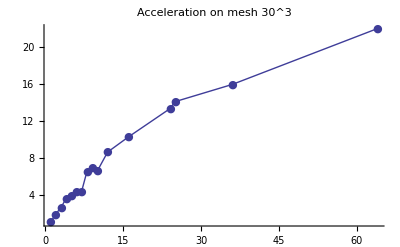
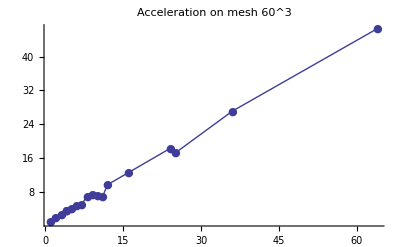
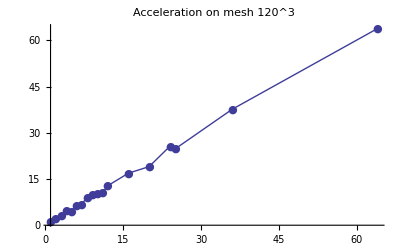

```mathematica
resIMM64=ReadData["result(IMM64).dat"];
grIMM64=ShowRel[#,True]&/@resIMM64
```

```mathematica
resIMM32=ReadData["result(IMM32).dat"];
ShowRel[#,True]&/@resIMM32
```

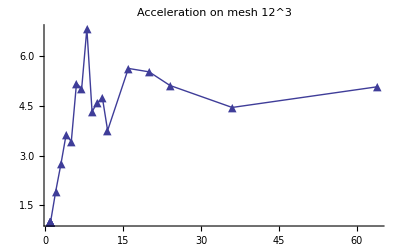
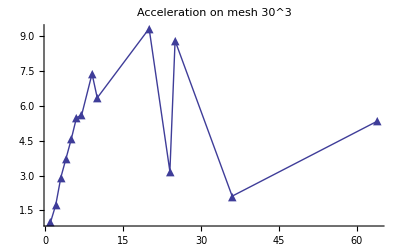
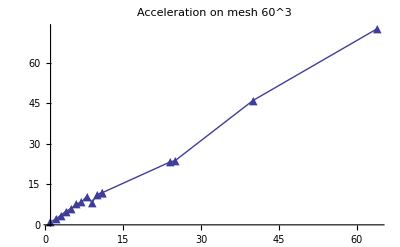
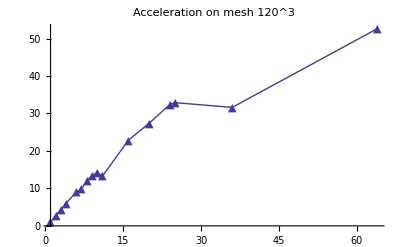

```mathematica
resPSTU=ReadData["result(PSTU).dat"];
grPSTU=ReplaceAll[ShowRel[#,True]&/@resPSTU,●->▲]
```

```mathematica
Manipulate[With[{list=ToExpression["res"<>cluster][[First@First@Position[{12,30,60,120},mesh]]]},ListLogLogPlot[{#⟦1⟧,(((#⟦4⟧)/(#⟦2⟧)#⟦1⟧)/(list⟦1,4⟧/list⟦1,2⟧))^-1}&/@list,PlotRange->All,AxesOrigin->{1,0},Filling->Axis]],
{cluster,{"Amazonka","Topsy","IMM64","PSTU"}},{mesh,{12,30,60,120}}]
```

Part::partd: Part specification resIMM64 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification resIMM64 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

Part::pspec: Part specification {2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧\ resIMM64 ⟦ 2 ⟧ ⟦ 1, 4 ⟧/2 ⟦ 1 ⟧\ 2 ⟦ 4 ⟧\ resIMM64 ⟦ 2 ⟧ ⟦ 1, 2 ⟧} is neither an integer nor a list of integers.

ListLogLogPlot::lpn: {resIMM64 ⟦ 1 ⟧, resIMM64 ⟦ 2 ⟧\ resIMM64 ⟦ 2 ⟧ ⟦ 1, 4 ⟧/resIMM64 ⟦ 1 ⟧\ resIMM64 ⟦ 4 ⟧\ resIMM64 ⟦ 2 ⟧ ⟦ 1, 2 ⟧} ⟦ {2 ⟦ 1 ⟧, 2 ⟦ 2 ⟧\ « 1 »/« 1 »} ⟧ is not a list of numbers or pairs of numbers.

```mathematica
Export["accel12.eps",Show[{grTopsy,grIMM64,grPSTU}⟦All,1⟧,PlotLabel->"12×12×12"]]
```

accel12.eps

```mathematica
Export["accel30.eps",Show[{grTopsy,grIMM64,grPSTU}⟦All,2⟧,PlotLabel->"30×30×30"]]
```

accel30.eps

```mathematica
Export["accel60.eps",Show[{grTopsy,grIMM64,grPSTU}⟦All,3⟧,PlotLabel->"60×60×60"]]
```

accel60.eps

```mathematica
Export["accel120.eps",Show[{grTopsy,grIMM64,grPSTU}⟦All,4⟧,PlotLabel->"120×120×120"]]
```

accel120.eps

```mathematica
(*Не хватает запусков на таких количествах процессов*)
Complement[Join[Range[12],{16,20,24,36,64}],Union[First/@#]]&/@resPSTU
```

{{},{8,11,12,16},{12,16,20,36},{5,12}}